## Tokenization

### Protein Tokenizer

```mathematica
proteinTokenVocabulary=<|
"A"->6,"R"->13,"N"->17,
"D"->14,"C"->23,"Q"->18,
"E"->9,"G"->7,"H"->22,
"I"->11,"L"->5,"K"->12,
"M"->21,"F"->19,"P"->16,
"S"->10,"T"->15,"W"->24,
"Y"->20,"V"->8,
(*all the unusual amino acids labeled with 25*)
"B"->25,"U"->25,"Z"->25,"O"->25,"J"->25|>;
```

```mathematica
{"A","B","C"}/.proteinTokenVocabulary
```

{6,25,23}

```mathematica
ProteinTokenizer[seq_String]:=Flatten[{2,Flatten[Characters/@StringSplit[seq]]/.proteinTokenVocabulary,3}]
```

```mathematica
ProteinTokenizer[seqBatch_List,length_Integer]:=Module[{tokens,paddedTokens,truncatedTokens,tokenTypeIDs,attentionMasks},
tokens=ProteinTokenizer/@seqBatch;
paddedTokens=PadRight[#,length]&/@tokens;
truncatedTokens=Take[#, Min[Length[#], length]]&/@paddedTokens;
tokenTypeIDs=Table[Table[0,length],Length[seqBatch]];
attentionMasks=(If[#!=0,1,0]&/@#)&/@truncatedTokens;
<|"input_ids"->truncatedTokens,
"token_type_ids"->tokenTypeIDs,
"attention_mask"->attentionMasks|>
]
```

```mathematica
testProtein=Entity["Protein","DEFB4"]
```

defensin, beta 4 precursor

```mathematica
ProteinData[testProtein,"MoleculePlot"]
```

-Graphics3D-

```mathematica
testProteinSequence=testProtein["Sequence"]
```

MRVLYLLFSFLFIFLMPLPGVFGGIGDPVTCLKSGAICHPVFCPRRYKQIGTCGLPGTKCCKKP

```mathematica
ProteinTokenizer[testProteinSequence]
```

{2,21,13,8,5,20,5,5,19,10,19,5,19,11,19,5,21,16,5,16,7,8,19,7,7,11,7,14,16,8,15,23,5,12,10,7,6,11,23,22,16,8,19,23,16,13,13,20,12,18,11,7,15,23,7,5,16,7,15,12,23,23,12,12,16,3}

### Molecule Tokenizer

```mathematica
moleculeTokenVocabulary=Association@@Import[FileNameJoin[{NotebookDirectory[],"SmilesTokenizer", "vocab.json"}]];
```

```mathematica
ImportMerges[filePath_String] := Module[{fileContent, parsedLines},
    (* Read file content *)
    fileContent = Import[filePath, "Lines"];
    (* Parse lines *)
    parsedLines = Select[fileContent, Not[StringStartsQ[#, "#"]] &];
    (* Split each line into a list and remove empty lines *)
    parsedLines = Select[StringSplit[parsedLines, Whitespace] , # =!= {} &];
    parsedLines
]
```

```mathematica
moleculeTokenMerges=ImportMerges[FileNameJoin[{NotebookDirectory[],"SmilesTokenizer", "merges.txt"}]];
```

```mathematica
MoleculeTokenizerMerger[tokens_List]:=Module[{currentTokens = tokens, currentMerge=moleculeTokenMerges[[1]], mergeIndex=1, index=1, pair, found=True}, 
	While[found==True,
		found=False;
		mergeIndex=1;
		(*Echo[currentTokens];*)
		While[mergeIndex<=Length[moleculeTokenMerges],
			currentMerge=moleculeTokenMerges[[mergeIndex]];
			mergeIndex=mergeIndex+1;
			index=1;
			While[index<=Length[currentTokens]-1,
				pair={currentTokens[[index]],currentTokens[[index+1]]};
				If[pair==currentMerge,
					currentTokens=Drop[currentTokens,{index,index+1}];
					currentTokens=Insert[currentTokens,StringJoin[pair],index];
					found=True
				];
				index=index+1
			];
			(*Echo[currentTokens];*)
		]
	];
	Return[currentTokens]
]
```

```mathematica
MoleculeTokenizerMerger[Characters@"CCCCCCCCCCCCCCCCCC(=O)O"]
```

{CCCCCCCC,CCCC,CCCCCC,(=,O,),O}

```mathematica
MoleculeTokenizer[smiles_String] := Module[{tokens,mergedTokens,translatedTokens},
	tokens=Characters[smiles];
	mergedTokens=MoleculeTokenizerMerger[tokens];
	translatedTokens=mergedTokens/.moleculeTokenVocabulary;
	Flatten[{0, translatedTokens, 2}]
]
```

```mathematica
MoleculeTokenizer[smilesBatch_List,length_Integer] := Module[{tokens,paddedTokens,truncatedTokens,attentionMasks},
	tokens=MoleculeTokenizer/@smilesBatch;
	paddedTokens=PadRight[#,length,1]&/@tokens;
	truncatedTokens=Take[#, Min[Length[#], length]]&/@paddedTokens;
	attentionMasks=(If[#!=1,1,0]&/@#)&/@truncatedTokens;
	<|"input_ids"->truncatedTokens,
	"attention_mask"->attentionMasks|>
]
```

```mathematica
testMolecule=Entity["Chemical","StearicAcid"];
```

```mathematica
MoleculePlot3D[testMolecule]
```

-Graphics3D-

```mathematica
testMoleculeSmiles=testMolecule["SMILES"]
```

CCCCCCCCCCCCCCCCCC(=O)O

```mathematica
MoleculeTokenizer[testMoleculeSmiles]
```

{0,693,285,365,263,51,13,51,2}

## Encoders

### Import Encoders

```mathematica
protEncoder=Import[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","prot_encoder.onnx"}],"NetExternalObject" ]
```

NetExternalObject[<>]

```mathematica
molEncoder=Import[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","mol_encoder.onnx"}],"NetExternalObject" ]
```

NetExternalObject[<>]

### Test Encoders

Using an epsilon of less than 1 e - 3, we verified the consistency of ChemBERTa' s and ProtBERT’s molecular encodings in the Wolfram Language against the same models using Python' s HuggingFace library, confirming near - identical outputs .

#### Molecule Encoder

```mathematica
testMolInput=MoleculeTokenizer[{"CCCCCCCCCCCCCCCCCCCC(=O)O"},278]
```

<|input_ids→{{0,693,693,285,263,51,13,51,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},attention_mask→{{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}|>

```mathematica
testMolOutput=molEncoder[testMolInput]
```

```mathematica
testMolOutput["909"] (*the pooled output*)
```

{{0.292658,-0.20106,-0.251445,0.276382,-0.594009,0.476731,0.401425,0.15805,-0.225795,-0.479353,-0.676519,0.0167246,0.945314,0.369727,0.37976,-0.204601,-0.106147,-0.376757,-0.189304,-0.239764,0.0083877,0.27116,-0.248269,0.242396,-0.651577,-0.107938,-0.294128,-0.175362,0.0448413,-0.0000927001,-0.100052,0.0517915,0.428531,-0.195184,-0.370192,-0.641025,0.645698,-0.336461,0.384874,-0.133838,0.0445861,0.611113,-0.233339,-0.511045,-0.324702,-0.0388828,0.226016,-0.267214,-0.714155,-0.0992147,-0.661447,-0.0670182,0.677118,0.445664,-0.614425,-0.740431,-0.369778,0.314676,0.586328,-0.699974,-0.840474,0.772373,0.606925,0.820182,0.600097,-0.000476479,-0.608032,-0.0116221,0.834027,0.273737,-0.387635,0.288504,-0.631127,-0.0578717,-0.443034,-0.689764,-0.0621992,-0.246238,-0.352318,0.14532,0.401849,0.0229072,0.480139,0.359451,0.443791,-0.00342319,0.515313,0.293592,-0.438546,-0.125707,0.250797,-0.133838,0.00439712,-0.428424,0.527317,-0.458679,0.650703,0.438726,0.907601,-0.520478,-0.16096,0.162397,0.62803,0.744367,-0.61717,-0.18278,-0.49924,-0.57683,-0.20259,0.115691,0.0462727,0.569509,-0.565277,0.278998,-0.469826,0.184598,-0.682102,0.601061,-0.38628,0.203339,0.208084,-0.491667,-0.0992427,0.0579455,0.150972,-0.00549367,0.666903,0.0638722,0.215484,-0.250685,0.243434,-0.626753,-0.759872,0.268554,-0.0444552,-0.28168,0.913637,-0.04082,-0.33919,0.602858,-0.27431,0.592924,0.241042,-0.457431,-0.0169452,0.172527,0.341045,-0.0533713,-0.0359777,-0.417921,0.029666,0.456025,0.791696,0.090871,0.460614,0.458095,-0.269141,0.255903,0.245077,0.582987,-0.369789,0.610656,0.216035,-0.596202,-0.647085,-0.293622,-0.094762,-0.308796,-0.681853,0.196919,0.520411,-0.254131,0.102038,0.360881,-0.323051,0.115711,0.172917,0.60481,0.291351,-0.454284,-0.486792,0.359142,0.118233,-0.658984,-0.249146,-0.527197,0.642132,0.758126,-0.339284,0.228365,-0.34633,0.295744,0.469549,-0.20308,0.046772,0.818708,-0.488803,0.414986,-0.450756,-0.141545,0.25151,-0.252739,0.782035,-0.636151,0.372105,0.354986,-0.884303,0.123911,-0.0945786,-0.242356,-0.674256,-0.610388,-0.176729,-0.668654,-0.278852,0.50805,-0.339206,0.0934895,0.376915,-0.0616154,0.116161,-0.687624,-0.257752,0.187954,-0.0696235,-0.234279,0.23471,0.276991,0.408353,-0.602059,-0.315594,-0.441483,0.0926246,-0.776038,0.752467,-0.347842,-0.291807,-0.136485,-0.563518,0.00765335,0.664983,-0.184692,0.0863143,0.596572,-0.658039,0.26182,-0.375837,-0.478254,0.397154,-0.175922,0.260413,0.178934,-0.0157612,0.0339322,-0.0642279,-0.120569,0.340198,0.300192,-0.355855,-0.39305,-0.88588,-0.0807504,-0.683821,0.577165,-0.88196,-0.428313,-0.19758,-0.528552,0.291762,0.737147,0.148741,-0.0367392,-0.133021,-0.693986,0.293202,-0.45998,0.558199,-0.182373,0.0471702,0.279737,-0.26873,-0.16112,0.793059,-0.759227,-0.660974,-0.0603252,0.292591,0.83814,0.0697678,0.296548,0.68221,-0.722229,-0.149176,-0.903419,-0.492951,0.399168,0.406832,-0.296604,0.269523,-0.368361,-0.344528,-0.252437,0.922517,0.425796,-0.230965,-0.230222,0.0342732,-0.558375,-0.174089,0.0202575,-0.0951281,-0.242919,0.61842,-0.652531,0.529807,0.640598,-0.69315,0.328767,-0.766244,0.170277,-0.139335,0.346748,0.297608,0.500549,0.146172,0.066819,-0.311818,-0.356101,0.4526,0.109068,0.884703,0.718469,0.370072,-0.390985,0.563956,-0.217727,-0.603468,0.179095,0.117231,0.248109,0.468434,0.187115,0.16246,-0.0757873,0.269496,0.00869851,-0.534904,0.406324,-0.712925,-0.379462,0.52616,0.111309,-0.675646,0.402594,-0.122109,-0.0113059,0.0750055,-0.338561,0.405544,-0.0932208,-0.636234,0.491998,0.110545,-0.26392,0.165193,0.276175,-0.300514,0.588144,0.00351471,-0.785048,-0.204925,0.601558,0.553866,0.0320534,0.127586,-0.70448,0.403375,-0.127902,0.52428,0.172534,-0.67519,-0.535293,0.442485,-0.0702344,0.681742,0.0460449,0.67626,-0.514102,-0.26933,-0.148716,0.839634,0.304564,-0.265907,0.349889,0.0316843,0.00524466,-0.666991,-0.32902,0.525203,-0.116802,0.760024,-0.401144,-0.08825,-0.384363,-0.793848,-0.239308,0.176219,0.31946,0.572676,0.148034,0.20495,0.771906,-0.47492,-0.0465054,-0.372379,-0.300598,-0.0395026,-0.387232,0.116155,-0.393404,-0.166774,-0.486825,-0.430362,0.232429,-0.166345,-0.0854879,0.0567312,-0.414025,-0.229405,-0.00447215,0.310647,-0.25698,0.624664,0.531898,-0.407414,0.55202,0.007632,-0.146486,-0.490812,0.831373,-0.497026,-0.461778,-0.28109,0.490697,0.648744,-0.814476,0.380585,-0.248781,-0.211701,-0.171031,0.173254,-0.0964997,0.436803,-0.311892,-0.160271,0.684726,-0.717514,-0.572902,-0.103368,-0.77214,0.271532,-0.47598,-0.595943,0.278032,0.121247,-0.269091,-0.351859,0.238215,0.366054,0.0864518,-0.0239787,-0.33021,0.82654,-0.50671,0.847089,0.344952,0.567953,-0.485583,-0.214265,0.547818,0.125313,-0.581096,-0.378833,0.771663,-0.425829,-0.210682,0.337395,-0.0508288,-0.582914,0.757174,0.763668,0.0422385,0.503455,-0.468313,0.144587,-0.61693,-0.452391,0.57888,-0.300084,-0.213211,-0.286834,-0.410051,0.157319,0.581523,-0.867164,0.370285,0.0591074,0.520186,0.404567,-0.640905,0.223108,-0.17763,0.0884091,0.391736,0.0291324,-0.38701,0.186855,-0.589717,0.294441,-0.505208,0.0422994,-0.238297,-0.0764462,0.212433,-0.390477,0.0150587,-0.0735417,0.626364,-0.0832883,-0.285233,0.786422,-0.375865,0.588011,0.553052,0.687384,0.0847437,0.019354,0.599509,0.697843,0.245997,-0.756301,0.288035,0.623378,-0.457025,-0.47392,0.376055,0.218747,0.655552,0.817556,0.718033,-0.684404,-0.0530716,-0.51707,0.363967,-0.446728,0.193591,0.430421,0.648155,-0.398441,0.383983,0.0770862,0.230443,-0.918481,-0.626648,0.213874,0.0782884,-0.074853,0.749077,-0.555684,-0.475691,-0.555873,-0.149497,0.0571759,0.162734,-0.633164,-0.0714957,-0.161204,0.137844,0.421977,-0.203973,-0.292138,-0.194535,0.162721,-0.213637,0.552216,-0.875785,0.416306,0.847338,-0.290922,0.282572,-0.775373,0.739049,0.60575,-0.454518,-0.818597,-0.409587,0.468995,-0.515738,0.70919,0.115144,0.391736,0.314145,0.548402,-0.105434,0.132176,0.759692,0.336721,-0.368084,0.159849,0.156197,0.194921,-0.716359,0.375134,0.0871041,-0.668405,0.26789,-0.711216,-0.43491,-0.281274,-0.486175,-0.0749438,-0.116956,-0.284355,-0.848094,-0.517137,-0.913029,0.245772,0.644785,0.59679,0.225634,-0.256806,0.194434,0.392417,-0.0999359,-0.540722,0.178523,-0.0902679,0.60166,0.491367,-0.89963,0.784627,0.499628,0.159213,-0.534029,-0.186526,0.749142,-0.772742,-0.559065,0.54732,0.0701066,0.401624,0.687156,0.266354,-0.349426,0.248228,-0.528663,-0.679059,0.236572,0.276909,0.234646,0.0732933,0.742494,0.476091,-0.114367,0.529009,0.113468,-0.676785,-0.422269,-0.358532,-0.783153,-0.0438065,-0.872192,-0.532059,-0.228729,-0.104651,0.493123,0.602559,0.0887726,-0.738616,-0.536694,-0.401862,-0.648152,0.000629678,-0.247793,0.62436,-0.318285,-0.855206,-0.38313,0.0409136,0.482006,-0.215267,-0.902624,-0.0278548,0.103221,0.131512,-0.534162,0.507948,-0.0758068,-0.102404,0.29667,-0.553803,-0.571841,-0.0322634,0.342489,0.660835,-0.256743,-0.241136,-0.751678,-0.313815,-0.258748,-0.42257,-0.0907716,-0.0728229,0.119237,-0.494346,-0.363591,-0.485334,0.286159,0.73003,0.159168,-0.549762,0.44801,0.578513,0.284542,-0.337307,-0.658205,-0.154765,0.117448,0.0720237,0.228264,0.39326,0.095315,0.590009,0.607415,0.17065,0.205119,0.259896,0.131771,0.322541,-0.0986492,-0.629183,0.506685,-0.816678,-0.111217,-0.36646,-0.600026,0.832903,0.492218,-0.445972,-0.673763,-0.821821,0.412006,0.184023,0.398225,0.811537,-0.229291,-0.728237,-0.552684,-0.0186505,-0.486056,-0.0875193,0.375775,-0.157298,-0.487303,0.20852,-0.660813,0.68942,0.565573}}

#### Protein Encoder

```mathematica
testProtInput=ProteinTokenizer[{"M T V P D R S E I A G K W Y V V A L A S N T E F F L R E K D K M K M A M A R I S F L G E D E L K V S Y A V P K P N G C R K W E T T F K K T S D D G E V Y Y S E E A K K K V E V L D T D Y K S Y A V I Y A T R V K D G R T L H M M R L Y S R S P E V S P A A T A I F R K L A G E R N Y T D E M V A M L P R Q E E C T V D E V"},3200];
```

```mathematica
testProtOutput=protEncoder[testProtInput]
```

```mathematica
testProtOutput["4195"] (*pooled output*)
```

{{-0.266408,0.281033,-0.253738,-0.268872,-0.287651,-0.281494,-0.279255,-0.276367,0.259644,-0.272238,0.274042,0.27738,-0.28003,0.256456,-0.268923,-0.283733,0.272042,0.256539,0.272658,-0.206858,-0.254051,-0.275655,-0.270453,-0.279601,0.23029,-0.278116,0.271548,0.277749,0.268275,0.260137,0.27498,0.27461,0.269122,-0.280321,0.252593,-0.269271,0.279694,-0.273376,0.275529,-0.278911,0.27299,-0.28469,0.237265,-0.275741,-0.275703,-0.279169,-0.274378,0.269267,0.27372,-0.280141,0.261611,-0.279985,0.278552,-0.270421,0.276931,-0.238959,0.265777,0.275334,0.278666,0.28357,0.268801,0.265298,-0.276116,0.278858,0.272447,0.277243,-0.269832,-0.270183,-0.265492,-0.268846,-0.219512,0.273404,0.280582,0.266084,0.271663,-0.26607,-0.275271,0.274412,0.26378,0.276956,-0.275989,-0.270326,-0.281036,0.271995,-0.274627,0.266263,0.281271,0.234091,-0.276339,-0.278645,-0.275185,0.25952,0.266426,0.286979,0.277203,0.235197,-0.270514,-0.279487,0.266997,-0.285007,0.28011,-0.275436,0.276727,0.264827,-0.275581,0.286009,-0.269122,-0.285997,0.285949,-0.264398,-0.272653,-0.277986,-0.228278,-0.285862,0.285524,-0.267535,-0.26518,-0.258656,-0.271453,0.273949,-0.282256,-0.279245,-0.283284,0.206848,-0.281991,-0.270922,-0.27465,0.278777,0.279246,-0.27065,0.271769,0.281273,0.225946,-0.276244,0.272807,-0.268216,0.280731,-0.253756,-0.265524,-0.279508,0.280701,-0.271192,-0.260671,0.276776,0.272091,0.281056,-0.258788,0.262485,0.266084,-0.266266,-0.27464,-0.266721,-0.27968,0.260207,-0.272857,0.237762,-0.272903,-0.264165,0.271921,-0.266443,0.269541,0.273762,-0.269926,0.27706,-0.264122,0.285015,0.27707,-0.278007,0.276447,0.234768,0.269183,-0.259553,0.278769,0.272834,-0.278112,0.264648,0.264069,-0.276084,0.28077,-0.253246,0.273084,0.276275,0.283932,-0.274803,-0.232315,-0.273294,-0.283516,0.239902,0.272768,0.227655,-0.268208,-0.265226,0.261553,0.274088,-0.273189,-0.279517,-0.259749,-0.267027,0.27327,0.281746,0.286304,0.283637,0.269418,0.261936,0.266368,-0.270778,0.277754,0.240086,-0.273993,-0.257709,0.271883,-0.271572,-0.27024,-0.269582,0.257708,0.273181,-0.27459,0.269441,-0.276844,0.274899,-0.276488,-0.286043,-0.282008,-0.275597,0.240962,-0.232195,0.273667,-0.256244,0.220304,0.267979,0.231059,-0.266595,-0.218492,-0.277541,-0.271215,-0.27397,-0.255623,0.254268,0.271695,-0.225721,-0.270697,-0.260125,-0.270315,0.27707,-0.273223,-0.270383,-0.260356,0.272602,-0.270145,0.27496,0.240369,-0.27962,-0.236177,-0.244689,0.279942,-0.277857,-0.265119,-0.283798,-0.277505,-0.288338,-0.265465,0.283831,-0.269638,-0.269994,0.274128,0.268813,-0.236822,0.2744,0.271867,0.27706,-0.260884,0.27708,-0.235683,-0.276938,0.287451,0.268252,-0.241963,0.272854,-0.270948,0.279662,0.240742,0.264962,-0.267065,-0.273588,-0.280632,-0.266918,-0.278415,0.220836,0.274085,0.268878,-0.271552,-0.262721,-0.27046,-0.278935,0.279614,-0.280034,0.264838,-0.27501,-0.277205,0.274919,0.272923,0.267236,-0.24491,-0.230842,-0.274211,-0.265543,0.278876,-0.274305,-0.229061,-0.269806,-0.278161,0.266471,-0.275002,0.276884,0.287612,-0.274206,0.266304,-0.274659,-0.279552,0.279694,-0.277951,0.260467,0.277746,0.260758,-0.238809,0.264456,-0.273308,-0.281997,-0.266392,0.281701,0.275179,0.274399,0.265215,0.270736,-0.280297,0.269034,0.272512,0.277497,0.276374,-0.273136,0.276836,-0.271699,0.267976,0.22155,-0.270119,0.254123,0.269067,-0.237325,0.271156,-0.276464,-0.271167,0.26286,-0.271628,-0.269571,-0.270698,-0.261539,0.26476,-0.264682,-0.271447,0.279346,-0.287943,-0.236229,-0.277309,-0.286756,0.277026,0.220446,0.283689,-0.270799,-0.260954,0.274581,0.256165,-0.272628,0.267693,0.281586,-0.270977,-0.273922,0.268898,-0.285829,0.282729,-0.276776,-0.26986,-0.294125,-0.279474,0.26892,0.225367,-0.240349,0.27826,0.268316,-0.270344,-0.281079,-0.277657,-0.226152,-0.278034,-0.270438,0.271179,0.275737,0.276868,-0.275243,0.266588,-0.268582,-0.278369,-0.267772,0.272605,0.278826,0.270639,-0.279946,0.277117,0.272448,0.237222,0.277977,0.273618,0.22561,-0.275395,0.23866,-0.273719,0.271513,-0.282144,-0.273434,-0.281819,0.281923,0.270672,0.240374,-0.275528,-0.273739,0.268058,0.280414,-0.262406,-0.271892,-0.232162,-0.269477,0.265178,-0.281967,-0.277117,0.276572,0.266535,-0.275986,0.273457,-0.276451,0.273456,-0.280662,-0.275536,0.269174,0.282742,-0.278924,-0.260256,-0.277395,-0.271444,0.232615,0.243833,0.279055,-0.278871,-0.274361,0.22081,-0.234761,-0.285045,0.273739,-0.274594,-0.28288,0.267997,-0.279263,-0.282964,-0.240971,-0.283026,0.236137,0.26357,0.262297,-0.277831,-0.219586,0.273907,0.26779,-0.276427,-0.241463,0.272619,0.281733,0.274381,-0.283845,0.256659,-0.263415,0.273457,0.272889,-0.277244,0.262919,-0.267003,0.252232,-0.271481,0.273404,-0.25886,0.228546,-0.284032,0.271573,-0.271605,-0.275704,-0.273968,-0.270699,0.268016,0.272518,0.265314,-0.272766,0.236092,0.273464,0.280153,0.250692,-0.274634,0.271752,0.272308,0.27928,-0.246622,-0.277874,0.271619,-0.272311,0.247046,-0.275718,-0.281705,-0.26907,-0.269085,-0.274724,0.277308,0.279172,-0.270895,-0.272486,0.266299,0.278142,-0.275074,-0.21795,-0.276245,0.276951,0.265124,-0.279619,-0.262866,-0.273757,0.230179,0.270897,-0.272006,0.275538,0.271209,-0.23731,-0.244265,0.269519,0.275027,-0.252228,0.267239,0.271908,0.268093,0.276544,0.263857,0.274471,-0.271493,-0.273289,0.266469,-0.274344,-0.214685,0.268288,-0.269077,0.229747,-0.284688,-0.245717,0.266544,-0.268504,-0.277755,-0.264213,0.278699,-0.269158,0.255456,0.276762,-0.26364,0.272722,-0.219679,-0.272805,0.271029,0.267667,0.282119,-0.267521,0.276694,0.272771,0.270175,-0.281494,0.248698,-0.278231,0.266912,-0.252065,-0.274628,-0.266262,0.281731,0.269223,-0.266702,-0.277552,0.268371,-0.219744,-0.27364,0.265968,0.278079,-0.262193,0.280629,0.263145,0.274397,0.201056,0.279457,0.273217,-0.276031,0.274212,-0.267166,-0.283007,0.254843,-0.279969,0.270593,0.27473,-0.277455,0.270467,0.28177,0.259296,0.233106,-0.277452,0.265885,0.27019,0.268871,-0.2664,0.275316,0.280612,0.27061,0.271216,0.228711,-0.266443,-0.275177,-0.27647,-0.270384,-0.22424,0.28241,0.278935,-0.270991,0.22309,0.237325,-0.277925,-0.273721,0.274989,-0.238538,0.27315,-0.280985,0.278248,-0.277749,0.274432,-0.277132,-0.271264,0.283595,0.268562,0.271922,0.267521,-0.274752,0.268792,-0.248588,-0.26892,0.27908,-0.197606,-0.282346,0.258144,0.270434,-0.27901,0.256592,0.276059,0.267134,0.280257,0.261338,0.231618,-0.269569,-0.234535,0.264604,-0.271041,0.252256,0.277353,-0.283181,-0.271122,-0.273373,0.276394,-0.231016,-0.263713,-0.27044,0.275703,0.273707,-0.278041,-0.277537,-0.271614,0.271867,-0.272915,0.262608,-0.275311,0.276713,0.292592,0.260666,-0.277911,0.265251,-0.276996,-0.27989,-0.279947,0.261795,-0.28052,-0.227074,0.237128,0.263029,0.282932,-0.274212,0.274133,-0.229704,0.273954,-0.2382,0.27346,-0.273221,0.272848,-0.254669,-0.275935,0.270092,-0.282799,-0.230448,-0.276215,0.270586,-0.273647,0.284264,-0.284142,0.270635,0.274091,0.270044,0.274339,-0.268539,0.271525,0.26823,0.273352,0.269444,-0.265335,-0.267599,-0.271323,-0.26833,-0.269346,-0.285839,0.273953,0.280145,-0.277815,-0.274803,-0.265204,0.271685,-0.262749,-0.265907,-0.267755,-0.239467,-0.275612,-0.268895,-0.268494,0.261448,0.270783,-0.273399,-0.236939,0.27336,0.277785,0.272715,0.274486,-0.266447,-0.233847,-0.272679,-0.282007,0.267701,0.258521,-0.260805,0.22008,0.240047,-0.258771,0.243005,-0.273764,-0.264364,0.279641,-0.228645,0.281728,0.284086,0.273492,-0.284176,-0.217555,0.266645,-0.269279,-0.239765,-0.260051,0.219017,-0.273208,0.199662,0.274377,0.273995,0.269514,-0.273004,0.274251,-0.275029,0.2736,-0.271453,-0.277526,0.276399,-0.27958,-0.231726,0.268868,0.268143,-0.273058,-0.27792,-0.269842,0.275469,0.283477,0.268119,0.266406,-0.279545,-0.282317,0.244708,-0.286022,-0.267302,-0.283873,-0.26641,0.257377,-0.224291,-0.264554,-0.278292,-0.233193,-0.281217,0.275457,0.275273,0.272857,0.273,-0.280335,-0.272659,0.276046,0.272084,-0.268586,-0.231769,-0.268266,0.273959,-0.259724,-0.283151,-0.274476,0.266119,-0.268992,-0.270324,-0.283093,0.274607,-0.261448,-0.231529,-0.275669,-0.274981,0.269512,0.274946,-0.269193,0.269499,0.252307,0.283542,0.271144,0.258588,0.28206,0.276474,-0.272803,-0.275273,0.281475,-0.286015,0.276723,0.27038,0.275005,-0.282991,0.271522,-0.270312,0.272107,-0.275596,-0.266572,-0.267332,0.278085,0.277768,0.274208,0.268071,-0.27576,0.272809,0.27189,-0.261765,0.274131,-0.285665,0.271416,0.273809,-0.265502,-0.265768,0.273309,0.277354,0.224334,-0.277644,0.281342,-0.272325,-0.265346,0.269178,0.278449,-0.277376,-0.276901,-0.268268,-0.246145,0.260869,0.275081,-0.272848,-0.282077,0.268531,-0.277299,-0.280302,0.273471,0.277628,-0.220953,-0.266234,-0.255785,0.271558,-0.274939,0.276475,-0.268994,0.274921,-0.258475,0.272919,0.267019,-0.281823,0.276045,-0.2701,0.27547,0.276307,0.28222,0.27281,0.219763,-0.270234,0.28191,0.275738,0.272919,0.275631,-0.268241,-0.271841,-0.232309,0.276167,0.276008,-0.231954,-0.278612,0.270793,-0.265643,0.276449,-0.266627,-0.277059,-0.286017,0.278663,0.280715,-0.276023,0.277766,0.275985,-0.274621,0.270092,-0.269423,0.271382,-0.264554,-0.270745,0.251585,0.277293,0.281734,0.273514,0.25795,-0.259704,0.278544,-0.227634,-0.285104,0.277445,-0.229887,-0.226999,-0.271303,0.270593,-0.283226,0.271644,-0.270092,-0.267344,0.266843,-0.260308,-0.281779,-0.271691,0.279102,-0.269741,-0.28558,-0.263068,-0.229515,0.255622,0.259426,0.277749,0.279668,-0.271481,-0.273229,-0.227754,0.22322,0.265585,0.264444,-0.272486,-0.268615,-0.265301,-0.279583,0.275238,0.282165,0.273502,0.268557,0.275011,0.272717,0.276906,-0.272658,0.268195,0.268629,-0.282502,0.262249,-0.283005,-0.269441,0.261346,0.269182,0.274656,-0.274978,0.271141,0.286119,0.277143,-0.255741,-0.229326,-0.275194,0.270563,-0.280633,-0.272242,0.271558,0.273075,-0.263804,0.278511,-0.276022,-0.273982,-0.257517,0.264326,0.268125,0.250876,-0.273684}}

## Dataset Creation

### Import Embeddings

```mathematica
dataRaw = Import[FileNameJoin[{$UserDocumentsDirectory, "WELP-PLAPT", "data", "tensor_dataset100k.json"}]];
dataRaw = Association @@ # & /@ dataRaw;
```

```mathematica
data = Dataset[dataRaw];
```

```mathematica
Length@data
```

100000

```mathematica
data[[1]]
```

### Prepare Data For Training

```mathematica
data = (Append[#, "concat_embeddings" -> Join[#["prot_embeddings"], #["mol_embeddings"]]]) & /@ data;
```

```mathematica
data[[1]]
```

```mathematica
train=RandomSample[data,Length[data]*0.9];
Length@train
```

90000

```mathematica
test=Complement[data,train];
Length@test
```

10000

```mathematica
trainInputs=Normal@train[All,"concat_embeddings"];
trainOutputs=Normal@train[All,"affinity"];
```

```mathematica
testInputs=Normal@test[All,"concat_embeddings"];
testOutputs=Normal@test[All,"affinity"];
```

## Model Creation

### Initialize Different Neural Networks

```mathematica
NetParameterCount[nnet_]:=Total[
	Times@@Dimensions[#]&/@Quiet[
		Select[
			Flatten[
				{Join[
					NetExtract[nnet,{All,"Weights"}],
					NetExtract[nnet,{All,"Biases"}]]}],
			Not[MissingQ[#]]&
		]
	]
]
```

#### Dense neural networks of different sizes

```mathematica
netDense238k=NetChain[{
LinearLayer[128],Ramp,
LinearLayer[64],Ramp,
LinearLayer[1]},
"Input"->1792,"Output"->"Scalar"];
netDense238k=NetInitialize[netDense238k]
NetParameterCount[netDense238k]
```

NetChain[<>]

237825

```mathematica
netDense2m=NetChain[{
LinearLayer[1024],Ramp,DropoutLayer[0.2],BatchNormalizationLayer[],
LinearLayer[160],Ramp,
LinearLayer[1]},
"Input"->1792,"Output"->"Scalar"];
netDense2m=NetInitialize[netDense2m]
NetParameterCount[netDense2m]
```

NetChain[<>]

2001217

```mathematica
netDense1214k=NetChain[{
LinearLayer[512],Ramp,DropoutLayer[0.2],BatchNormalizationLayer[],
LinearLayer[512],Ramp,DropoutLayer[0.2],BatchNormalizationLayer[],
LinearLayer[64],Ramp,
LinearLayer[1]},
"Input"->1792,"Output"->"Scalar"];
netDense1214k=NetInitialize[netDense1214k]
NetParameterCount[netDense1214k]
```

NetChain[<>]

1214593

#### Branching neural network

```mathematica
netBranching=NetGraph[
{"ProtOnly"->PartLayer[1;;1024],
"MolOnly"->PartLayer[1025;;1792],
"ProtLinear"->LinearLayer[512],"ProtRamp"->Ramp,
"MolLinear"->LinearLayer[512],"MolRamp"->Ramp,
"Combined"->ThreadingLayer[Plus],"Normalize"->BatchNormalizationLayer[],
"Linear1"->LinearLayer[512],"Ramp1"->Ramp,"Dropout1"->DropoutLayer[0.2],
"Linear2"->LinearLayer[64],"Ramp2"->Ramp,
"FinalLinear"->LinearLayer[1]},
{NetPort["Input"]->"ProtOnly"->"ProtLinear"->"ProtRamp",NetPort["Input"]->"MolOnly"->"MolLinear"->"MolRamp",{"ProtRamp","MolRamp"}->
"Combined"->"Normalize"->
"Linear1"->"Ramp1"->
"Dropout1"->
"Linear2"->"Ramp2"->"FinalLinear"->NetPort["Output"]},"Input"->1792,"Output"->"Scalar"
];
netBranching=NetInitialize[netBranching]
```

NetGraph[<>]

### Train Neural Networks

```mathematica
TrainingProtocol[net_,trainInputs_,trainOutputs_,testInputs_,testOutputs_]:=NetTrain[
	net,
	<|"Input"->trainInputs,"Output"->trainOutputs|>,
	LossFunction->MeanSquaredLossLayer[],
	BatchSize->32,
	MaxTrainingRounds->60,
	ValidationSet-><|"Input"->testInputs,"Output"->testOutputs|>,
	TrainingProgressReporting->"Panel",
	WorkingPrecision->"Real32",
	TargetDevice->"GPU"
]
```

#### Training dense neural networks

```mathematica
trainedDense238k=TrainingProtocol[netDense238k];
trainedDense2m=TrainingProtocol[netDense2m];
trainedDense1214k=TrainingProtocol[netDense1214k];
```

#### Training branching neural network

```mathematica
trainedBranching=TrainingProtocol[netBranching,trainInputs,trainOutputs,testInputs,testOutputs]
```

NetGraph[<>]

```mathematica
meanSquaredError=Mean[Power[testOutputs-trainedBranching[testInputs],2]]
```

0.629843

#### Export trained model

```mathematica
Export[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","affinity_predictor.onnx"}],trainedBranching]
```

C:\Users\tatwo\Documents\WELP-PLAPT\models\affinity_predictor.onnx

```mathematica
plapt=trainedBranching
```

## Model Importing (Alternative to Model Creation)

```mathematica
plapt=Import[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","affinity_predictor.onnx"}]]
```

NetGraph[<>]

## Model Inference

### Inverse Normalization

```mathematica
scalingParams =
  <|"mean" -> 6.51286529169358,
   "var" -> 2.4379994951935378,
   "scale" -> 1.5614094578916633|>;
```

```mathematica
Denormalize[normalizedAffinity_, params_Association] := (normalizedAffinity*params["scale"] + params["mean"])
```

### Inference

```mathematica
PredictAffinityNormalized[nnet_, molecule_String, protein_String] := Module[{molTokens, protTokens, molEmbeddings, protEmbeddings, affinity},
  molTokens = MoleculeTokenizer[{molecule}, 278];
  protTokens = ProteinTokenizer[{protein}, 3200];
  molEmbeddings = molEncoder[molTokens][["909"]];
  protEmbeddings = protEncoder[protTokens][["4195"]];
  nnet[Flatten[Join[protEmbeddings, molEmbeddings]]]
  ]
```

```mathematica
PredictAffinity[nnet_, molecule_String, protein_String] := Module[{molTokens, protTokens, molEmbeddings, protEmbeddings, affinityNormalized, affinity},
    molTokens = MoleculeTokenizer[{molecule}, 278];
    protTokens = ProteinTokenizer[{protein}, 3200];
    molEmbeddings = molEncoder[molTokens][["909"]];
    protEmbeddings = protEncoder[protTokens][["4195"]];
    affinityNormalized = nnet[Flatten[Join[protEmbeddings, molEmbeddings]]];
    <|"neg_log10_affinity_M"->Denormalize[affinityNormalized,scalingParams],
    "affinity_uM"->10^6*10^(-Denormalize[affinityNormalized,scalingParams])|>
]
```

```mathematica
PredictAffinityNormalized[nnet_,molecule_,protein_]:=PredictAffinityNormalized[nnet,molecule["SMILES"],protein["Sequence"]]
```

```mathematica
PredictAffinity[plapt,"ABC","DEF"]
```

<|neg_log10_affinity_M→{4.63541},affinity_uM→{23.1521}|>

## Analysis

```mathematica
xValuesUnseen=Flatten[Denormalize[#,scalingParams]&/@plapt[testInputs]];
yValuesUnseen=Denormalize[#,scalingParams]&/@testOutputs;
```

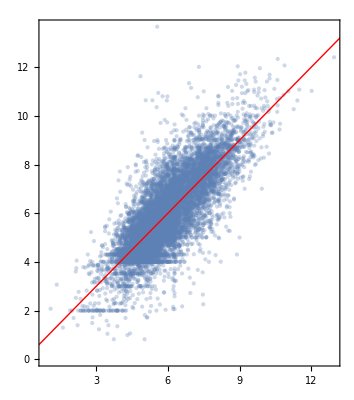

0.79562

```mathematica
Show[
ListPlot[Transpose[{xValues,yValues}],PlotStyle->{PointSize[Medium],Opacity[0.3]},PlotRange->All,AspectRatio->{1},Frame->True],
Plot[x,{x,-20,20},PlotStyle->{Red,Thick}],AspectRatio->{1}]

Correlation[xValues,yValues]
```

```mathematica
xValuesTrain=Flatten[Denormalize[#,scalingParams]&/@plapt[trainInputs]];
yValuesTrain=Denormalize[#,scalingParams]&/@trainOutputs;
```

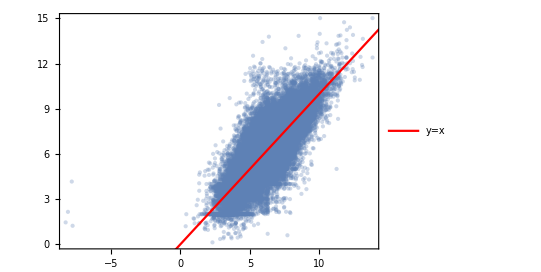

0.799263

```mathematica
Show[
ListPlot[Transpose[{xValuesTrain,yValuesTrain}],PlotStyle->{PointSize[Medium],Opacity[0.3]},PlotRange->All,AspectRatio->{1},Frame->True],
Plot[x,{x,-20,20},PlotStyle->{Red,Thick},PlotLegends->{"y=x","Best Fit Line"}],AspectRatio->{1}]

Correlation[xValuesTrain,yValuesTrain]
```